```mathematica
SensorLinB1r[g_] := Module[{mmIni,mmIniPairs,gn1,nodesp, nodesn,temp,temp2, gbipartite,maxmatching, gml,  NumberOfNodes, sensors, sensorswhere, sensorslin},
mmIni =FindIndependentEdgeSet[Graph[RandomSample[EdgeList[g]]]];
mmIniPairs=Partition[mmIni,1]/.{x_-> y_}->{x,y};
gn1 = EdgeDelete[g,mmIni];
nodesp=ToString[#]<>"p"&/@VertexList[gn1]; 
nodesn=ToString[#]<>"n"&/@VertexList[gn1];
(* create edges for the bipartite graph, e.g., 1->2 corresponds to 1p <-> 1n *)
temp=Partition[EdgeList[gn1],1]/.{x_-> y_}->{x,y} ;
temp2={ToString[#[[1]]]<>"p",ToString[#[[2]]]<>"n"}&/@temp;
gbipartite=Graph[Join[Join[RandomSample[nodesp], RandomSample[nodesn]]],Flatten[temp2/.{x_,y_}->{x<->y}] , VertexLabels->"Name", GraphLayout->"BipartiteEmbedding"]; 
maxmatching=FindIndependentEdgeSet[gbipartite];
gml=VertexList[Graph[maxmatching]];
NumberOfNodes=VertexCount[gn1];sensorswhere=Table[FreeQ[gml,ToString[i]<>"p" ],{i,1,NumberOfNodes}];sensorslin=Flatten[Position[sensorswhere,True]];
sensors = If[Length[sensorslin]==0, RandomInteger[{1,NumberOfNodes}],sensorslin]; 
sensors
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
parameterDir="Community_parameters/";
dataDir = "data/dataSave/";
```

```mathematica
samples = 5000; (*number of MSS*)
fn = "M_SD_020"; (*WoL ID*)
```

## get data

```mathematica
CasesN = Flatten[{Range[1,18],"o",19}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,o,19}

```mathematica
A=Transpose[Import[parameterDir<>fn<>"_Abin_0.csv", "Table"] ];
G = DirectedGraph[AdjacencyGraph[Transpose[A]]];
speciesl= VertexList[G];
EWScore = Table[Flatten[Import[dataDir<>fn<>"_detection100_"<>ToString[i]<>".csv", "Table"]],{i,CasesN}];
(*EWScore0 = Flatten[Import[dataDir<>fn<>"_detection0_o.csv", "Table"]];*)
```

## calculate sensor score

```mathematica
MSS= Table[SensorLinB1r[G],{samples}]; 
SensorScore= N[Table[Length[Position[MSS, speciesl[[i]]]]/samples,{i,VertexCount[G]}]];
```

```mathematica
SetSize = Ceiling[Mean[Table[Length[MSS[[i]]],{i,1,samples}]]];
```

## correlation tests

```mathematica
Table[{CasesN[[i]],SpearmanRankTest[EWScore[[i]],SensorScore,{"TestData"}]} ,{i,1,Length[EWScore]}](*with competition*)
```

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

{{1,{{0.343789,0.00823465}}},{2,{{0.627724,1.33586×10^-7}}},{3,{{0.472761,0.000178708}}},{4,{{0.343817,0.00822918}}},{5,{{0.166549,0.211468}}},{6,{{Indeterminate,Indeterminate}}},{7,{{0.292785,0.0257232}}},{8,{{-0.00637247,0.962134}}},{9,{{0.272789,0.0382891}}},{10,{{0.198008,0.136236}}},{11,{{0.668195,9.99519×10^-9}}},{12,{{0.612958,3.14389×10^-7}}},{13,{{0.780205,5.23209×10^-13}}},{14,{{0.664256,1.30904×10^-8}}},{15,{{0.645605,4.45424×10^-8}}},{16,{{Indeterminate,Indeterminate}}},{17,{{Indeterminate,Indeterminate}}},{18,{{Indeterminate,Indeterminate}}},{o,{{0.720925,1.74928×10^-10}}},{19,{{0.607456,4.27714×10^-7}}}}

## Comparison Plots

```mathematica
dataEWSS=Table[Transpose@{EWScore[[i]], SensorScore},{i,1,Length[EWScore]}];
```

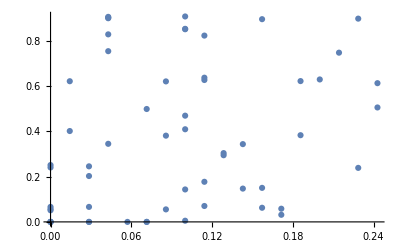
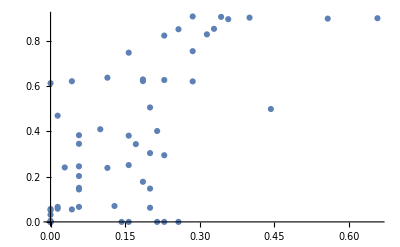
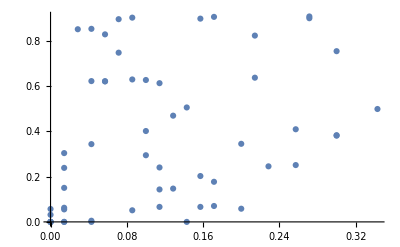
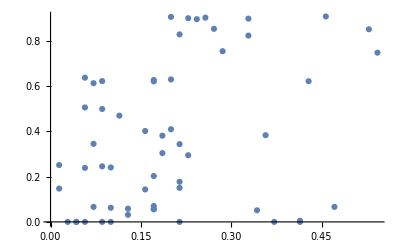
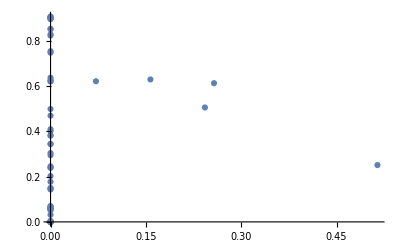
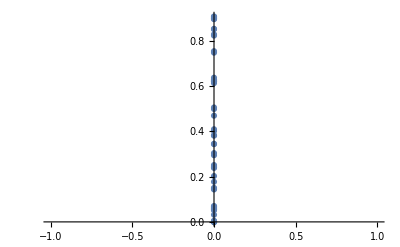
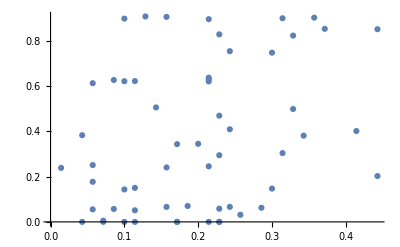
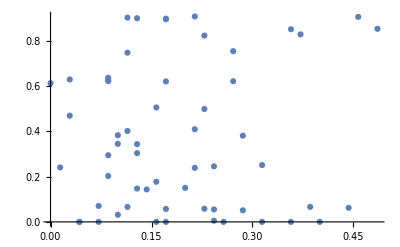
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-},{11,-Graphics-},{12,-Graphics-},{13,-Graphics-},{14,-Graphics-},{15,-Graphics-},{16,-Graphics-},{17,-Graphics-},{18,-Graphics-},{o,-Graphics-},{19,-Graphics-}}

```mathematica
Table[{CasesN[[i]],ListPlot[dataEWSS[[i]]]},{i,1,Length[EWScore]}]
```

```mathematica
OrderS=Reverse[Ordering[SensorScore]];
OrderS66 = OrderS[[1;;Ceiling[2*SetSize/3]]];
OrderS33 = OrderS[[1;;Ceiling[SetSize/3]]];
MaxEW = Table[Max[EWScore[[i]]],{i,1,Length[EWScore]}];
LabelsRF={"33%", "66%", "100%"};
```

```mathematica
Rf = Table[{Max[EWScore[[i]][[OrderS33]]]/MaxEW[[i]], Max[EWScore[[i]][[OrderS66]]]/MaxEW[[i]], Max[EWScore[[i]][[OrderS]]]/MaxEW[[i]]}
,{i,1,Length[EWScore]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

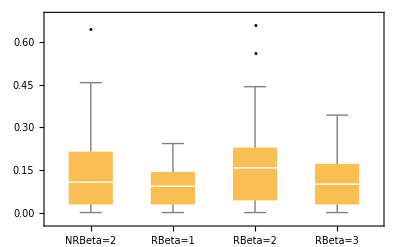

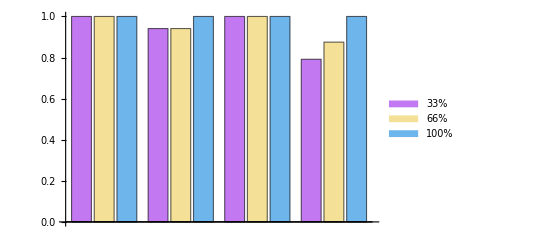

```mathematica
CasesBR = {19,1,2,3};
LabelsBr = {"NRBeta=2", "RBeta=1", "RBeta=2","RBeta=3"};
BoxWhiskerChart[EWScore[[CasesBR]],"Outliers", ChartLabels->LabelsBr]
BarChart[Rf[[CasesBR]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

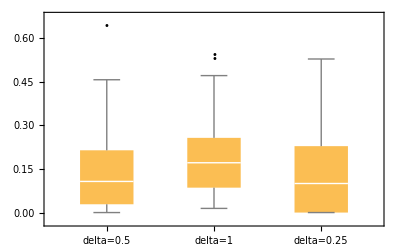

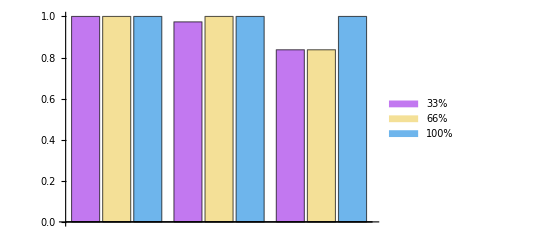

```mathematica
CasesD = {19,4,20};
LabelsD = {"delta=0.5", "delta=1",  "delta=0.25"};
BoxWhiskerChart[EWScore[[CasesD]],"Outliers", ChartLabels->LabelsD]
BarChart[Rf[[CasesD]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

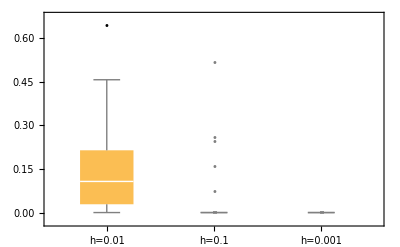

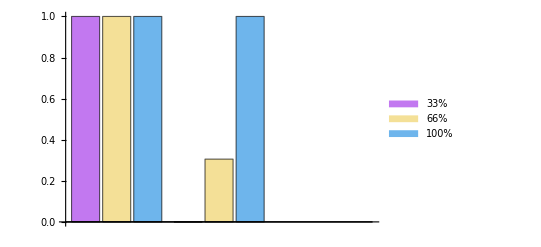

```mathematica
CasesH = {19,5,6};
LabelsBr = {"h=0.01", "h=0.1", "h=0.001"};
BoxWhiskerChart[EWScore[[CasesH]],"Outliers", ChartLabels->LabelsBr]
BarChart[Rf[[CasesH]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

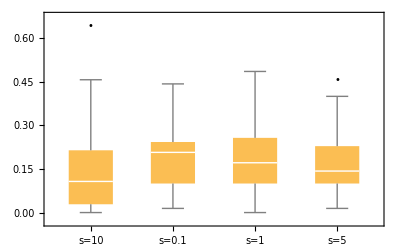

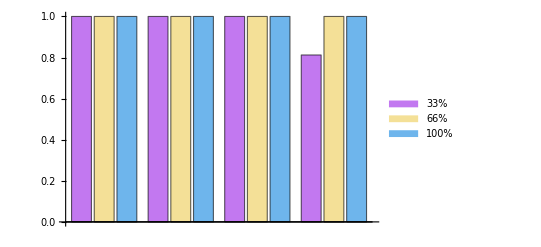

```mathematica
CasesS = {19,7,8,9};
LabelsBr = {"s=10", "s=0.1", "s=1","s=5"};
BoxWhiskerChart[EWScore[[CasesS]],"Outliers", ChartLabels->LabelsBr]
BarChart[Rf[[CasesS]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

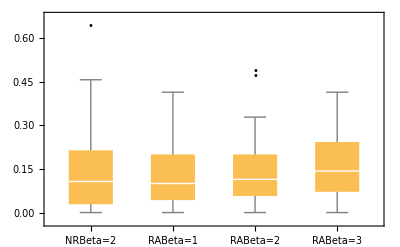

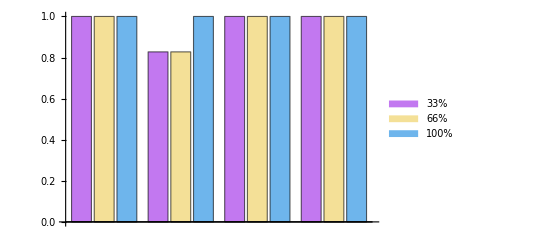

```mathematica
CasesBA = {19,10, 11, 12};
LabelsBr = {"NRBeta=2", "RABeta=1", "RABeta=2","RABeta=3"};
BoxWhiskerChart[EWScore[[CasesBA]],"Outliers", ChartLabels->LabelsBr]
BarChart[Rf[[CasesBA]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

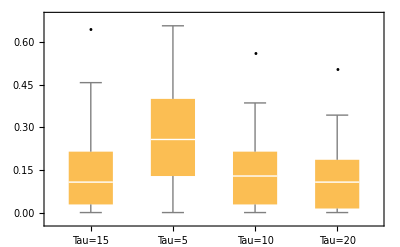

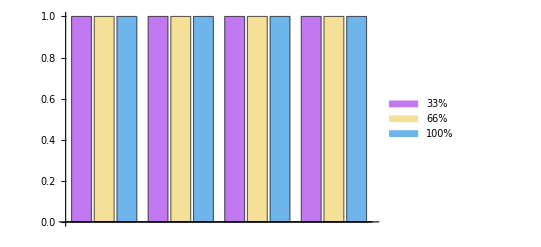

```mathematica
CasesT = {19,13, 14, 15};
LabelsBr = {"Tau=15", "Tau=5", "Tau=10","Tau=20"};
BoxWhiskerChart[EWScore[[CasesT]],"Outliers", ChartLabels->LabelsBr]
BarChart[Rf[[CasesT]],ChartStyle->"Pastel", ChartLegends->LabelsRF]
```

## plot parameters and data

```mathematica
or2 = Ordering[SensorScore];
c2=Table[ColorData["Rainbow"][i],{i,0,1,1/(Length[or2]-1)}];
c2o=Table[c2[[Flatten[Position[or2,i]]]],{i,Length[or2]}];
animals=Position[A[[1]],_?(#>= 1&)][[1]][[1]]-1;
vs=Table[i-> "Diamond",{i,animals}];
dataEWSS=Transpose@{10*EWScore, SensorScore};
Fitt=FindFit[dataEWSS,{a/(1+b*Exp[-c (x-d)])},{a,b,c,d},x];
FitData=Table[a/(1+b*Exp[-c (x-d)])/.Fitt,{x,0,7}];
(*dataEWSS0=Transpose@{10*EWScore0, SensorScore};*)
```

## plots

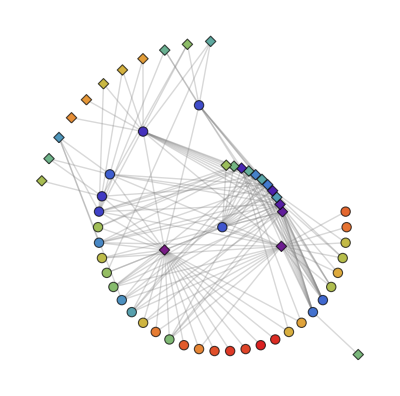

```mathematica
Gp = UndirectedGraph[AdjacencyGraph[Transpose[A]],
GraphLayout->"RadialEmbedding",
VertexStyle->Thread[Range[Length[c2o]]->c2o],
VertexSize->1.2,EdgeStyle->Opacity[0.3, Gray],
VertexShapeFunction->vs]
```

```mathematica
o
```

## EW Score vs Sensor Score

Part::take: Cannot take positions 26 through 0 in ….

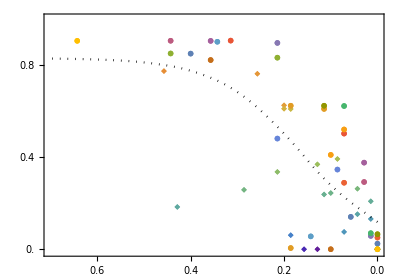

```mathematica
Show[
ListPlot[Flatten[{dataEWSS[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{0,7},{-0.01,1}},
ScalingFunctions->{"Reverse",Automatic},(*FrameTicks->{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"}},Automatic}, *)
FrameTicks->{{Range[0,2,0.2],None},{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"},{7,"0.7"}},None}}, 
AxesOrigin->{5,0}]
, 
ListPlot[Flatten[{dataEWSS[[animals+1;;Length[dataEWSS]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataRepeatS2]]],PlotMarkers->{●,Small},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{"w_i","sensor score"},
Ticks->{{{2,"0.2"},{4,"0.4"},{6,"0.6"}},Automatic}]
,
ListPlot[Transpose@{Range[8]-1,FitData},Joined->True,InterpolationOrder->2,ScalingFunctions->{"Reverse",Automatic},PlotRange->{Automatic,{0,1}},PlotStyle->{Black,Dotted},AxesLabel->{"w_i","sensor score"}]
]
```

## Vertex degree vs Sensor Score

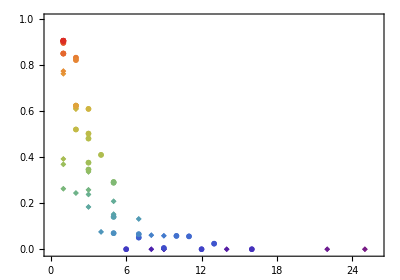

```mathematica
dataDegreedScore = Transpose@{VertexDegree[Gp],SensorScore};
Show[ListPlot[Flatten[{dataDegreedScore[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{-.02,26},{-0.01,1}}],
ListPlot[Flatten[{dataDegreedScore[[animals+1;;Length[dataDegreedScore]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataDegreedScore]]],PlotMarkers->{●,Small}]]
```

## Compare the EW score with and without competition

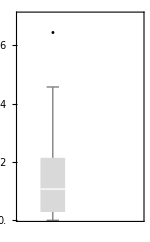

```mathematica
BoxWhiskerChart[{EWScore,EWScore0},"Outliers",
AspectRatio->GoldenRatio,
ImageSize->150,
FrameStyle->Black,
FrameTicksStyle->12,
ImageSize->{Automatic,220},
PlotRange->{Automatic,{0.01,0.7}},
FrameTicks->{{Range[0,1,0.1],None},{Range[0,1,0.2],None}},
ChartStyle->LightGray
]
```

## EW Score vs Sensor Score without competition

```mathematica
Show[
ListPlot[Flatten[{dataEWSS0[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{0,4},{-0.01,1}},
ScalingFunctions->{"Reverse",Automatic},(*FrameTicks->{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"}},Automatic}, *)
FrameTicks->{{Range[0,2,0.2],None},{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"}},None}}]
, 
ListPlot[Flatten[{dataEWSS0[[animals+1;;Length[dataEWSS0]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataRepeatS20]]],PlotMarkers->{●,Small},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{"w_i","sensor score"},
Ticks->{{{2,"0.2"},{4,"0.4"},{6,"0.6"}},Automatic}]
]
```

Part::take: Cannot take positions 1 through 25 in Transpose[{10 Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«11»,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}].

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in {Transpose[{10 Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«11»,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}]⟦«1»⟧}.

Transpose::nmtx: The first two levels of {10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,0.3682,«9»,0.,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}} cannot be transposed.

Part::take: Cannot take positions 1 through 25 in Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«11»,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}].

Flatten::flpi: Levels to be flattened together in {2.} should be lists of positive integers.

Transpose::nmtx: The first two levels of {10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,0.3682,«9»,0.,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}} cannot be transposed.

Part::take: Cannot take positions 1 through 25 in Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«11»,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}].

General::stop: Further output of Part::take will be suppressed during this calculation.

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in {Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«12»,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}]⟦1;;25⟧}.

Transpose::nmtx: The first two levels of {10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,0.3682,«9»,0.,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Flatten::flpi: Levels to be flattened together in {2.} should be lists of positive integers.

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in {Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,«12»,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}]⟦1;;25⟧}.

General::stop: Further output of Flatten::fldep will be suppressed during this calculation.

ListPlot::lpn: Flatten[{Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,«13»,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}]⟦1;;25⟧},«1»] is not a list of numbers or pairs of numbers.

Flatten::flpi: Levels to be flattened together in {2.} should be lists of positive integers.

General::stop: Further output of Flatten::flpi will be suppressed during this calculation.

ListPlot::lpn: Flatten[{Transpose[{10. Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,«13»,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,«8»}}]⟦1;;25⟧},«1»] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Flatten[{Transpose[{Times[«2»],{«58»}}]⟦1;;25⟧},{2}],«9»,FrameTicks→{{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.},None},{{{0,0.0},{1,0.1},{2,0.2},{3,0.3},{4,0.4}},None}}],ListPlot[Flatten[{Transpose[{Times[«2»],{«58»}}]⟦26;;1⟧},{2}],«4»,Ticks→{«1»}]].

Show[ListPlot[Flatten[{Transpose[{10 Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,0.3682,0.2438,0.3916,0.761,0.7726,0.0242,0.0052,0.,0.0506,0.0578,0.,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,0.9048,0.48,0.5194,0.9042,0.6212,0.8484,0.6224,0.849}}]⟦1;;25⟧},{2}],PlotStyle→{{RGBColor[0.471412, 0.108766, 0.527016]},{RGBColor[0.42640091228070176, 0.11124010526315789, 0.5655992982456141]},{RGBColor[0.3813898245614035, 0.11371421052631579, 0.6041825964912281]},{RGBColor[0.3363787368421053, 0.11618831578947368, 0.6427658947368421]},{RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334]},{RGBColor[0.3036508070175439, 0.13081933333333334, 0.6773248070175438]},{RGBColor[0.2645751929824562, 0.47786245614035083, 0.8034802280701755]},{RGBColor[0.35473673684210527, 0.6483712105263157, 0.6555840000000001]},{RGBColor[0.2745003157894737, 0.5074873684210526, 0.7892946842105264]},{RGBColor[0.39211880701754387, 0.6767825087719298, 0.5976280350877193]},{RGBColor[0.30879063157894737, 0.5892688947368421, 0.73472]},{RGBColor[0.3726487719298246, 0.6638449649122806, 0.6272058596491229]},{RGBColor[0.2867155087719298, 0.16108066666666668, 0.7067095087719297]},{RGBColor[0.47822752631578946, 0.7181006315789473, 0.4826352631578948]},{RGBColor[0.5530944736842105, 0.7357296842105263, 0.4061161052631579]},{RGBColor[0.8871974736842105, 0.6152267894736841, 0.22391852631578948]},{RGBColor[0.8296354385964911, 0.6955225087719298, 0.24848364912280702]},{RGBColor[0.41158884210526314, 0.6897200526315789, 0.5680502105263159]},{RGBColor[0.45476787719298245, 0.7102210526315789, 0.5106041052631579]},{RGBColor[0.7898378947368421, 0.722286052631579, 0.2628467894736842]},{RGBColor[0.6059977719298246, 0.7434759298245613, 0.3600282456140351]},{RGBColor[0.43130822807017544, 0.7023414736842105, 0.5385729473684211]},{RGBColor[0.6606158596491228, 0.7431050701754386, 0.3262713157894737]},{RGBColor[0.8977243508771929, 0.5905404736842105, 0.2182983157894737]},{RGBColor[0.9013688947368421, 0.5579578947368421, 0.21180852631578947]},{RGBColor[0.24536294736842104, 0.33502417543859647, 0.8070269473684211]},{RGBColor[0.24722905263157893, 0.29688915789473685, 0.7938530526315789]},{RGBColor[0.2697802105263158, 0.191342, 0.7360942105263157]},{RGBColor[0.24601350877192982, 0.3722439298245614, 0.8148949649122808]},{RGBColor[0.2583879649122807, 0.4426562807017544, 0.8072851403508773]},{RGBColor[0.2528449122807018, 0.22160333333333332, 0.7654789122807018]},{RGBColor[0.25220073684210526, 0.4074501052631579, 0.811090052631579]},{RGBColor[0.24909515789473685, 0.2587541403508772, 0.7806791578947369]},{RGBColor[0.6332791578947369, 0.7434214210526315, 0.34295089473684215]},{RGBColor[0.28567140350877196, 0.5352518596491228, 0.7716489298245615]},{RGBColor[0.7395861052631579, 0.7343186140350877, 0.28436987719298246]},{RGBColor[0.5795461228070176, 0.7396028070175439, 0.3830721754385965]},{RGBColor[0.6879525614035088, 0.7427887192982456, 0.3095917368421053]},{RGBColor[0.5266428245614035, 0.7318565614035087, 0.4291600350877193]},{RGBColor[0.29684249122807016, 0.5630163508771929, 0.7540031754385965]},{RGBColor[0.33942136842105264, 0.6286704385964912, 0.6819626666666667]},{RGBColor[0.8102774035087719, 0.7096662280701754, 0.25529487719298244]},{RGBColor[0.9024013157894737, 0.48561431578947367, 0.19803842105263159]},{RGBColor[0.5016871754385965, 0.7259802105263158, 0.4546664210526316]},{RGBColor[0.8880922280701754, 0.3580744561403509, 0.17320484210526316]},{RGBColor[0.9018851052631579, 0.5217861052631578, 0.20492347368421052]},{RGBColor[0.8811459824561403, 0.3129499649122807, 0.16435347368421055]},{RGBColor[0.869007, 0.2221106315789474, 0.14804547368421053]},{RGBColor[0.874831, 0.26761294736842106, 0.1560042105263158]},{RGBColor[0.8661437192982455, 0.6645994210526316, 0.23515894736842105]},{RGBColor[0.857359, 0.131106, 0.132128]},{RGBColor[0.7144602105263158, 0.7403348947368421, 0.29513142105263157]},{RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334]},{RGBColor[0.863183, 0.17660831578947367, 0.14008673684210526]},{RGBColor[0.8489934736842105, 0.6813787894736842, 0.24167242105263156]},{RGBColor[0.9019847192982456, 0.4483234385964912, 0.1909075789473684]},{RGBColor[0.876670596491228, 0.6399131052631579, 0.22953873684210527]},{RGBColor[0.8950384736842105, 0.40319894736842105, 0.1820562105263158]}},Frame→True,FrameStyle→GrayLevel[0],FrameTicksStyle→12,PlotMarkers→{◆,Large},AspectRatio→0.7,ImageSize→{Automatic,220},PlotRange→{{0,4},{-0.01,1}},ScalingFunctions→{Reverse,Automatic},FrameTicks→{{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.},None},{{{0,0.0},{1,0.1},{2,0.2},{3,0.3},{4,0.4}},None}}],ListPlot[Flatten[{Transpose[{10 Flatten[$Failed],{0.,0.,0.,0.,0.1314,0.,0.0584,0.152,0.061,0.208,0.0752,0.1834,0.,0.2624,0.3354,0.6242,0.6094,0.2376,0.2576,0.6082,0.3682,0.2438,0.3916,0.761,0.7726,0.0242,0.0052,0.,0.0506,0.0578,0.,0.0558,0.,0.3756,0.0652,0.5016,0.3456,0.4092,0.2916,0.0696,0.1404,0.6086,0.8308,0.2884,0.8948,0.8206,0.8998,0.9038,0.9036,0.6224,0.9048,0.48,0.5194,0.9042,0.6212,0.8484,0.6224,0.849}}]⟦26;;1⟧},{2}],PlotStyle→{{RGBColor[0.471412, 0.108766, 0.527016]},{RGBColor[0.42640091228070176, 0.11124010526315789, 0.5655992982456141]},{RGBColor[0.3813898245614035, 0.11371421052631579, 0.6041825964912281]},{RGBColor[0.3363787368421053, 0.11618831578947368, 0.6427658947368421]},{RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334]},{RGBColor[0.3036508070175439, 0.13081933333333334, 0.6773248070175438]},{RGBColor[0.2645751929824562, 0.47786245614035083, 0.8034802280701755]},{RGBColor[0.35473673684210527, 0.6483712105263157, 0.6555840000000001]},{RGBColor[0.2745003157894737, 0.5074873684210526, 0.7892946842105264]},{RGBColor[0.39211880701754387, 0.6767825087719298, 0.5976280350877193]},{RGBColor[0.30879063157894737, 0.5892688947368421, 0.73472]},{RGBColor[0.3726487719298246, 0.6638449649122806, 0.6272058596491229]},{RGBColor[0.2867155087719298, 0.16108066666666668, 0.7067095087719297]},{RGBColor[0.47822752631578946, 0.7181006315789473, 0.4826352631578948]},{RGBColor[0.5530944736842105, 0.7357296842105263, 0.4061161052631579]},{RGBColor[0.8871974736842105, 0.6152267894736841, 0.22391852631578948]},{RGBColor[0.8296354385964911, 0.6955225087719298, 0.24848364912280702]},{RGBColor[0.41158884210526314, 0.6897200526315789, 0.5680502105263159]},{RGBColor[0.45476787719298245, 0.7102210526315789, 0.5106041052631579]},{RGBColor[0.7898378947368421, 0.722286052631579, 0.2628467894736842]},{RGBColor[0.6059977719298246, 0.7434759298245613, 0.3600282456140351]},{RGBColor[0.43130822807017544, 0.7023414736842105, 0.5385729473684211]},{RGBColor[0.6606158596491228, 0.7431050701754386, 0.3262713157894737]},{RGBColor[0.8977243508771929, 0.5905404736842105, 0.2182983157894737]},{RGBColor[0.9013688947368421, 0.5579578947368421, 0.21180852631578947]},{RGBColor[0.24536294736842104, 0.33502417543859647, 0.8070269473684211]},{RGBColor[0.24722905263157893, 0.29688915789473685, 0.7938530526315789]},{RGBColor[0.2697802105263158, 0.191342, 0.7360942105263157]},{RGBColor[0.24601350877192982, 0.3722439298245614, 0.8148949649122808]},{RGBColor[0.2583879649122807, 0.4426562807017544, 0.8072851403508773]},{RGBColor[0.2528449122807018, 0.22160333333333332, 0.7654789122807018]},{RGBColor[0.25220073684210526, 0.4074501052631579, 0.811090052631579]},{RGBColor[0.24909515789473685, 0.2587541403508772, 0.7806791578947369]},{RGBColor[0.6332791578947369, 0.7434214210526315, 0.34295089473684215]},{RGBColor[0.28567140350877196, 0.5352518596491228, 0.7716489298245615]},{RGBColor[0.7395861052631579, 0.7343186140350877, 0.28436987719298246]},{RGBColor[0.5795461228070176, 0.7396028070175439, 0.3830721754385965]},{RGBColor[0.6879525614035088, 0.7427887192982456, 0.3095917368421053]},{RGBColor[0.5266428245614035, 0.7318565614035087, 0.4291600350877193]},{RGBColor[0.29684249122807016, 0.5630163508771929, 0.7540031754385965]},{RGBColor[0.33942136842105264, 0.6286704385964912, 0.6819626666666667]},{RGBColor[0.8102774035087719, 0.7096662280701754, 0.25529487719298244]},{RGBColor[0.9024013157894737, 0.48561431578947367, 0.19803842105263159]},{RGBColor[0.5016871754385965, 0.7259802105263158, 0.4546664210526316]},{RGBColor[0.8880922280701754, 0.3580744561403509, 0.17320484210526316]},{RGBColor[0.9018851052631579, 0.5217861052631578, 0.20492347368421052]},{RGBColor[0.8811459824561403, 0.3129499649122807, 0.16435347368421055]},{RGBColor[0.869007, 0.2221106315789474, 0.14804547368421053]},{RGBColor[0.874831, 0.26761294736842106, 0.1560042105263158]},{RGBColor[0.8661437192982455, 0.6645994210526316, 0.23515894736842105]},{RGBColor[0.857359, 0.131106, 0.132128]},{RGBColor[0.7144602105263158, 0.7403348947368421, 0.29513142105263157]},{RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334]},{RGBColor[0.863183, 0.17660831578947367, 0.14008673684210526]},{RGBColor[0.8489934736842105, 0.6813787894736842, 0.24167242105263156]},{RGBColor[0.9019847192982456, 0.4483234385964912, 0.1909075789473684]},{RGBColor[0.876670596491228, 0.6399131052631579, 0.22953873684210527]},{RGBColor[0.8950384736842105, 0.40319894736842105, 0.1820562105263158]}}⟦26;;0⟧,PlotMarkers→{●,Small},ScalingFunctions→{Reverse,Automatic},AxesLabel→{w_i,sensor score},Ticks→{{{2,0.2},{4,0.4},{6,0.6}},Automatic}]]